```mathematica
(*Define parameters*)
K=1; (*Kerr nonlinearity*)
P=5; (*Two-photon drive strength*)
nMax=10; (*Maximum number of photons in the Fock basis*)

(*Create the annihilation operator*)
a=SparseArray[{{n_,m_}/;n==m+1->Sqrt[m]},{nMax,nMax}];
(*Create the creation operator*)
ad=Transpose[a];

(*Define the Hamiltonian H=K/2*a†^2 a^2-P/2*(a^2+a†^2)*)
H=-K*ad.ad.a.a+P*(a.a+ad.ad);
```

```mathematica
{eigenvalues, eigenstates}=Eigensystem[N[H]];
```

```mathematica
groundstate=eigenstates[[-1]]
```

{0.69465,0.,0.608514,0.,0.285356,0.,-0.0285633,0.,-0.25481,0.}

```mathematica
(*Define the Wigner function*)
WignerFunction[psi_,{x_,y_}]:=1/(2 Pi) Integrate[Exp[-I p y] (Conjugate[psi[x+I y]] psi[x-I y]),{p,-10,10}];

(*Discretize phase space*)xRange=Range[-5,5,0.1];
yRange=Range[-5,5,0.1];

(*Compute the Wigner function on a grid*)
wignerValues=Table[WignerFunction[groundstate,{x,y}],{x,xRange},{y,yRange}];
```

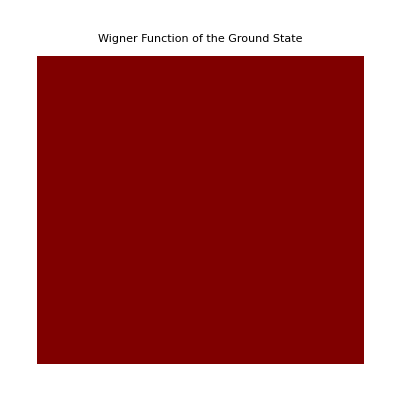

```mathematica
(*Plot the Wigner function*)ArrayPlot[wignerValues,ColorFunction->"Rainbow",PlotRange->All,FrameLabel->{"X","Y"},PlotLabel->"Wigner Function of the Ground State"]
```